```mathematica
ClearAll[generateKeyWithPlot]
generateKeyWithPlot[seed_Integer]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,traj1,traj2,traj3,timeSteps,positions,keyData,binaryKeyData,flattenedBinaryKey,randomSequence,key},(*Initial conditions*)pos1={0,0};
vel1={0,10}*conv;
SeedRandom[seed];
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};
(*Differential equations*)eq={x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};
(*Initial conditions for solver*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve system*)sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];
(*Extract trajectories*)traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;
(*Sample positions*)timeSteps=Range[0,100,0.1];
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];
(*Convert to binary*)keyData=Flatten[positions];
binaryKeyData=IntegerDigits[Round[Abs[keyData]*10^6],2,24];
flattenedBinaryKey=Flatten[binaryKeyData];
(*XOR with PRBS*)randomSequence=RandomInteger[{0,1},Length[flattenedBinaryKey]];
key=BitXor[flattenedBinaryKey,randomSequence];
(*Print info*)Print["Seed: ",seed];
Print["Key length: ",Length[key]];
Print["Counts: ",Counts[key]];
(*Plot trajectories*)Print[ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotLegends->{"Particle 1","Particle 2","Particle 3"},AxesLabel->{"x (au)","y (au)"},PlotRange->All,ImageSize->Large]];

(*Return key*)
key]
```

Seed: 12

Key length: 144144

Counts: <|0→71829,1→72315|>

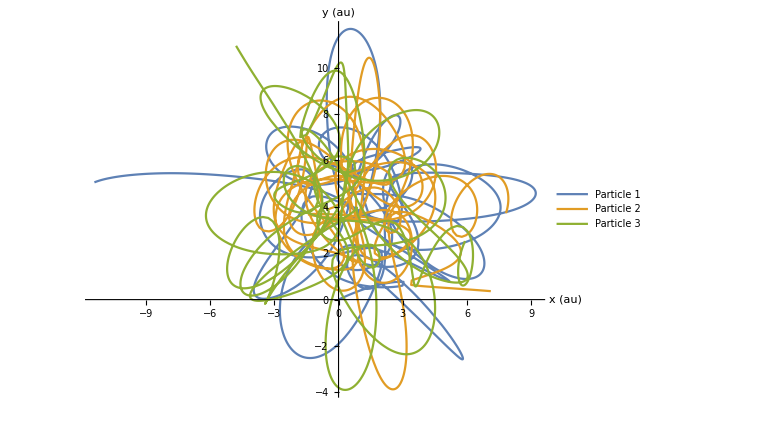

Seed: 22

Key length: 144144

Counts: <|1→72244,0→71900|>

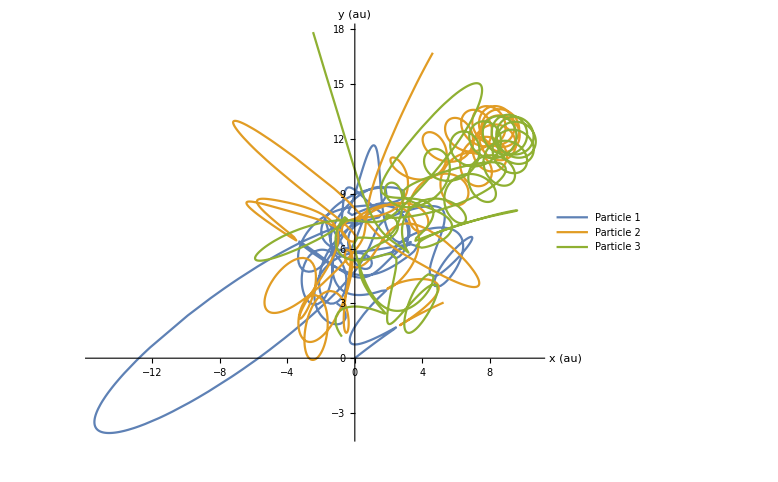

XOR key length: 144144

XOR key counts: <|1→71945,0→72199|>

```mathematica
key1=generateKeyWithPlot[12];
key2=generateKeyWithPlot[22];

len=Min[Length[key1],Length[key2]];
key=BitXor[key1[[;;len]],key2[[;;len]]];

Print["XOR key length: ",len];
Print["XOR key counts: ",Counts[key]];
```

```mathematica
(*SerialRandomnessTest*)
serialResult=N@ResourceFunction["SerialRandomnessTest"][key,"TestStatistic"];
serialPValue=N@ResourceFunction["SerialRandomnessTest"][key,"PValue"];
Print["Serial Randomness Test:"];
Print["  Test Statistic: ",serialResult];
Print["  P-Value: ",serialPValue];
If[serialPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ChiSquareRandomnessTest*)
chiSquareResult=N@ResourceFunction["ChiSquareRandomnessTest"][key,"TestStatistic"];
chiSquarePValue=N@ResourceFunction["ChiSquareRandomnessTest"][key,"PValue"];
Print["\nChi-Square Randomness Test:"];
Print["  Test Statistic: ",chiSquareResult];
Print["  P-Value: ",chiSquarePValue];
If[chiSquarePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*BinaryRunRandomnessTest*)
binaryRunResult=N@ResourceFunction["BinaryRunRandomnessTest"][key,"TestStatistic"];
binaryRunPValue=N@ResourceFunction["BinaryRunRandomnessTest"][key,"PValue"];
Print["\nBinary Run Randomness Test:"];
Print["  Test Statistic: ",binaryRunResult];
Print["  P-Value: ",binaryRunPValue];
If[binaryRunPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ArcsineLawRandomnessTest*)
arcsineResult=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"TestStatistic"];
arcsinePValue=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"PValue"]; (*Force numeric evaluation*)
Print["\nArcsine Law Randomness Test:"];
Print["  Test Statistic: ",arcsineResult];
Print["  P-Value: ",arcsinePValue];
If[arcsinePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];
```

Serial Randomness Test:

Test Statistic: 0.841303

P-Value: 0.643647

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.44758

P-Value: 0.503486

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 71950.

P-Value: 0.521199

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.414259

P-Value: 0.890289

Result: Good randomness (p-value > 0.05)

```mathematica
generateSBoxFromKey[key_List]:=Module[{chunks,values,sbox,plot},(*1. Partition into 8-bit blocks*)chunks=Partition[key,8];
(*2. Convert each block to decimal*)values=FromDigits[#,2]&/@chunks;
(*3. Extract first 256 unique values*)sbox=DeleteDuplicates[values];
sbox=Take[sbox,256];
(*4. Check length*)If[Length[sbox]<256,Print["⚠️ Not enough unique values to form a full S-box!"];
Return[$Failed];];
(*5. Print S-box*)Print["✅ S-box generated (length = ",Length[sbox],"):"];
Print[sbox];
(*6. Visualize as 16×16 grid*)plot=ArrayPlot[Partition[sbox,16],ColorFunction->"Rainbow",Frame->True,Mesh->True,PlotLabel->"S-box Visualization",ImageSize->Large];
Print[plot];
(*7. Return S-box*)sbox];
```

S-box generated (length = 256):

{236,210,14,224,50,104,159,219,247,163,91,160,197,66,120,250,41,122,182,180,234,254,137,126,21,132,239,25,143,199,45,118,46,55,88,97,102,240,35,113,138,192,96,127,54,218,7,195,237,203,133,242,57,227,134,177,94,31,83,173,68,205,193,249,73,214,67,241,221,105,245,121,69,107,223,119,222,141,142,6,246,36,135,81,82,251,13,238,16,98,106,200,229,140,230,194,171,60,202,74,169,206,47,165,198,116,244,183,49,56,27,153,186,44,12,208,152,59,99,77,24,30,248,179,188,175,63,149,58,212,61,53,5,17,189,217,150,144,166,253,95,176,18,109,211,255,213,216,84,93,123,151,201,72,191,20,220,110,129,29,86,2,23,124,43,232,155,228,252,3,52,10,168,101,1,37,125,87,76,112,114,115,4,85,172,131,146,215,167,178,75,158,38,80,145,92,108,28,9,147,32,40,233,70,0,34,64,130,8,139,128,79,161,22,62,209,39,207,184,204,15,90,154,19,185,51,156,225,111,164,181,226,103,162,148,11,190,48,231,78,196,71,187,33,243,89,42,65,136,157,174,26,235,117,100,170}

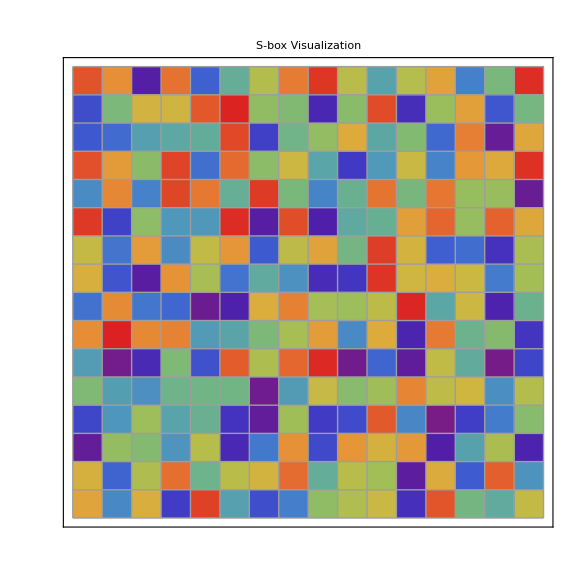

S-box generated (length = 256):

{88,198,101,108,129,141,103,174,195,104,229,106,221,137,72,130,50,241,19,79,23,160,11,107,7,25,206,187,157,179,191,200,138,253,71,220,120,132,218,53,95,228,162,217,148,125,91,255,208,249,124,213,59,5,57,111,172,222,93,231,237,69,254,33,21,112,24,128,230,82,48,68,67,177,126,99,204,150,45,251,143,16,75,201,109,14,170,36,51,9,131,166,188,17,39,22,73,196,78,42,248,87,240,13,85,149,159,122,233,110,197,155,83,26,3,234,76,252,81,225,156,192,190,227,119,35,199,232,134,70,44,245,29,116,235,144,8,92,64,60,203,215,242,194,180,247,100,86,121,244,152,163,46,183,12,123,1,193,173,117,66,20,250,184,115,2,239,135,211,113,61,168,246,186,212,62,147,145,142,38,56,210,80,89,178,6,84,47,102,40,27,209,185,34,114,165,226,224,74,18,158,136,105,15,161,54,140,63,0,146,58,243,90,96,49,176,154,219,214,169,189,207,164,205,175,171,41,118,32,97,151,216,167,31,37,77,4,28,55,202,94,43,181,98,153,10,127,52,139,30,65,238,236,223,133,182}

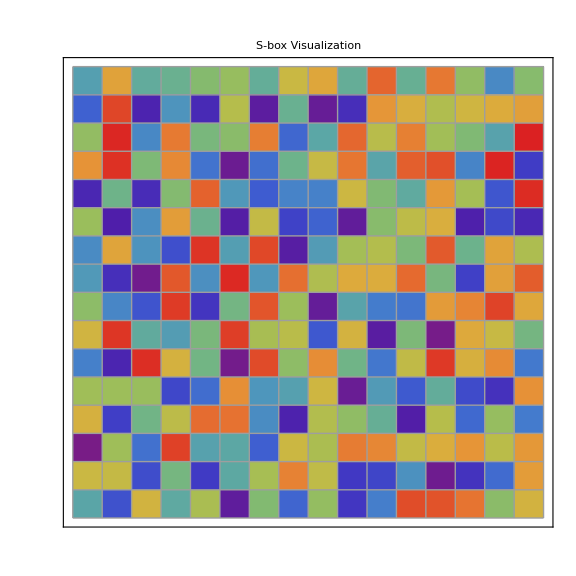

S-box generated (length = 256):

{152,153,59,218,202,236,160,67,57,58,201,205,246,34,77,25,109,203,14,29,69,80,159,119,138,102,182,212,154,206,82,37,89,99,238,103,23,168,76,33,101,120,207,85,87,78,198,45,183,52,252,140,19,208,92,48,165,91,28,18,225,13,100,197,253,54,187,237,181,11,96,55,228,31,51,35,43,191,196,5,66,123,22,242,162,178,49,254,61,64,68,95,211,93,16,41,161,136,4,70,44,27,235,107,231,24,53,157,155,224,190,249,167,135,134,193,32,204,56,215,88,230,38,12,139,125,243,239,30,158,47,142,50,216,83,84,3,104,229,21,10,177,180,74,114,184,143,36,108,117,124,240,248,209,26,126,213,90,141,72,63,106,62,255,163,7,97,221,192,151,199,232,214,98,81,200,116,222,79,2,65,133,250,210,110,188,9,179,185,156,94,226,86,40,73,118,194,8,112,129,169,132,60,149,241,166,186,146,171,0,220,105,111,174,217,245,46,251,173,195,6,164,115,175,227,130,131,233,189,122,234,137,172,71,1,42,144,219,147,127,39,148,121,176,223,113,128,20,145,150,170,75,15,244,247,17}

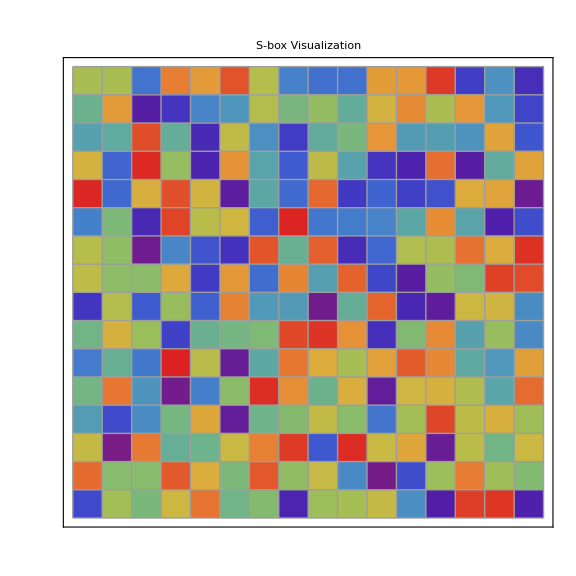

```mathematica
chunkSize=Floor[Length[key]/3];
keyParts={key[[1;;chunkSize]],key[[chunkSize+1;;2 chunkSize]],key[[2 chunkSize+1;;3 chunkSize]]};

(*Assign each S-box to a named variable*)
sbox1=generateSBoxFromKey[keyParts[[1]]];
sbox2=generateSBoxFromKey[keyParts[[2]]];
sbox3=generateSBoxFromKey[keyParts[[3]]];
```

```mathematica
ClearAll[EvalSboxWithReport]
EvalSboxWithReport[sbox_]:=Module[{sboxBitCount,sboxBitsLists,sboxBitLvlsList,NaturalBasis,walshM,nonLin,SACRes2D,calBitVal,sac,bic,lap,DifList2D,dap},(*Setup*)sboxBitCount=Log2[Length[sbox]];
sboxBitsLists=Table[IntegerDigits[sbox[[i]],2,sboxBitCount],{i,Length[sbox]}];
sboxBitLvlsList=Table[Table[sboxBitsLists[[i]][[j]],{i,Length[sbox]}],{j,sboxBitCount}];
(*Walsh matrix*)
NaturalBasis[s_]:=With[{u={{1,1},{1,-1}}},Nest[ArrayFlatten[#/. {1->u,-1->-u}]&,{{1}},s]];
walshM=NaturalBasis[sboxBitCount];
(*Nonlinearity*)
nonLin=Max[Table[2^(sboxBitCount-1)-Max[Abs[Drop[sboxBitLvlsList[[i]].walshM,1]]],{i,Length[sboxBitLvlsList]}]];
(*SAC matrix*)
SACRes2D=Table[Table[0,{i,sboxBitCount}],{j,sboxBitCount}];
calBitVal[m_,n_,testVal_]:=BitAnd[IntegerPart[testVal/(2^n)],1];

For[m=0,m<sboxBitCount,m++,For[i=0,i<=Length[sbox]-1,i++,For[n=0,n<sboxBitCount,n++,SACRes2D[[m+1]][[n+1]]+=calBitVal[m,n,BitXor[sbox[[i+1]],sbox[[BitXor[i,2^m]+1]]]]]]];
(*SAC average*)sac=Total[Total[SACRes2D/(2^sboxBitCount)]]/sboxBitCount^2;
(*BIC*)bic=2^(sboxBitCount-1)-Max[Abs[2^(sboxBitCount-1)-Flatten[SACRes2D]]];
(*LAP*)lap=Max[Abs[(Flatten[SACRes2D]/2^(sboxBitCount))-0.5]];
(*DAP*)DifList2D=Table[0,{i,(2^sboxBitCount)}];

For[i=1,i<=Length[sbox],i++,For[j=1,j<=Length[sbox],j++,DifList2D[[i]]+=((sbox[[i]]-sbox[[j]]))]];
dap=1/Mean[Abs[DifList2D/2^(sboxBitCount)]];
(*Optimal reference values*)
maxNonLin=2^(sboxBitCount-1)-2^(sboxBitCount/2-1);(*theoretical max*)idealSAC=0.5;
idealLAP=0;
idealDAP=1;

(*Print report*)
Print["Bits per entry: ",sboxBitCount];
Print["----------------------------------"];
Print["Nonlinearity: ",nonLin," (max theoretical: ",maxNonLin,")"];
Print["SAC (Strict Avalanche): ",NumberForm[N[sac],{3,2}]," (ideal: ",idealSAC,")"];
Print["BIC (Bit Independence): ",bic];
Print["LAP (Linear Approx.): ",NumberForm[N[lap],{3,2}]," (ideal: ",idealLAP,")"];
Print["DAP (Differential Approx.): ",NumberForm[N[dap],{3,2}]," (ideal: ",idealDAP,")"];
Print["----------------------------------"];
(*Return metrics as list*){nonLin,sac,bic,lap,dap}];
```

```mathematica
EvalSboxWithReport[sbox1];
EvalSboxWithReport[sbox2];
EvalSboxWithReport[sbox3];
```

Bits per entry: 8

----------------------------------

Nonlinearity: 106 (max theoretical: 120)

SAC (Strict Avalanche): 0.50 (ideal: 0.5)

BIC (Bit Independence): 96

LAP (Linear Approx.): 0.13 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------

Bits per entry: 8

----------------------------------

Nonlinearity: 106 (max theoretical: 120)

SAC (Strict Avalanche): 0.50 (ideal: 0.5)

BIC (Bit Independence): 96

LAP (Linear Approx.): 0.13 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------

Bits per entry: 8

----------------------------------

Nonlinearity: 108 (max theoretical: 120)

SAC (Strict Avalanche): 0.52 (ideal: 0.5)

BIC (Bit Independence): 100

LAP (Linear Approx.): 0.11 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------